```mathematica
f
```

```mathematica
EulersMethod[x0_, y0_, h_, halt_] :=
Module[{x = x0, y = y0, j, points={{x0,y0}} },
For[j = 1, j ≤ halt, j++,
y = y + h*f[x, y];
x = x + h;
points = Append[points, {x, y}]];
Return[points]];
```

```mathematica
solapprox = EulersMethod[0, 1, 0.1, 20]
```

{{0,1},{0.1,1.1},{0.2,1.21},{0.3,1.331},{0.4,1.4641},{0.5,1.61051},{0.6,1.77156},{0.7,1.94872},{0.8,2.14359},{0.9,2.35795},{1.,2.59374},{1.1,2.85312},{1.2,3.13843},{1.3,3.45227},{1.4,3.7975},{1.5,4.17725},{1.6,4.59497},{1.7,5.05447},{1.8,5.55992},{1.9,6.11591},{2.,6.7275}}

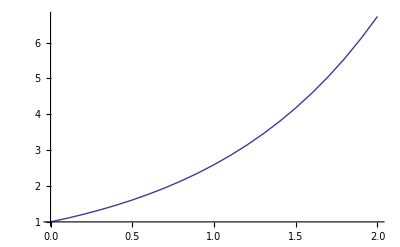

```mathematica
Papprox = ListPlot[solapprox, Joined -> True, PlotStyle -> Thick]
```

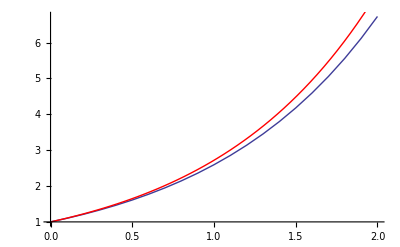

```mathematica
Ptrue = Plot[Exp[x], {x, 0, 2}, PlotStyle -> {Thick, Red}];
Show[Papprox, Ptrue]
```